## Formulae an

```mathematica
ExplainContractionCounts[g_,e_]:=Block[{
gBis=SortGraph[g], 
taken={e[[1]],e[[2]]},
comp=SortGraph[VertexDelete[VertexDelete[GraphComplement[g],e[[1]]],e[[2]]]],
nonEdges=0,
remainingNonEdges=0,
result},
result=Table[
If[!EdgeQ[gBis,e[[1]]<->v]&&!EdgeQ[gBis,e[[2]]<->v],
nonEdges++
]
,{v,Select[VertexList[gBis],!MemberQ[taken,#]&]}
];
remainingNonEdges=Length[EdgeList[comp]];
{nonEdges,remainingNonEdges}
]
```

```mathematica
MpgChain[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain[contract],{e,ChromaticPolynomial[g,4]/24}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
MpgChain3[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain3[contract],ChromaticPolynomial[g,4]/24];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
Monitor[Select[Table[k->With[{l=Differences[Reverse[MpgChain3[ReadGrof[k]]]]},{Min[l],Max[l]}],{k,10}],#[[2]]≠{0,0}&],k]
```

{4→{0,3},6→{0,3},7→{0,3}}

```mathematica
cm=72/2.54;
```

```mathematica
MakeComplete[v_]:=Map[SortEdge[#[[1]]<->#[[2]]]&,Subsets[v,{2}]]
```

```mathematica
MakeComplete[Range[3]]
```

{1<->2,1<->3,2<->3}

```mathematica
BeautiGraph[g_]:=Graph[MakeComplete[VertexList[g]],GraphHighlight->EdgeList[GraphComplement[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name", EdgeStyle->LightGray]
```

```mathematica
SolGraph[g_,sol_,newNeighbors_:{},highlight_:{}]:=Block[{
s=SymbolToSets[sol],
edges={},
colors={Red,Blue,Yellow,Green}, 
color=1,
high=Map[SortEdge,EdgeList[GraphComplement[g]]],
taken,
vertices={},
nonedges,
interesting,
 blackEdges
},
interesting=Select[VertexList[g],MemberQ[newNeighbors,#]&];
blackEdges=Map[#->Directive[Black,Thickness[0.01]]&,MakeComplete[interesting]];
nonedges=Length[high];
Table[
edges=Join[edges,Map[#->Directive[colors[[color]],Thick]&,MakeComplete[block]]];
vertices=Join[vertices,Map[#->colors[[color]]&,block]];
color+=1
,{block, s}
];
taken=Map[SortEdge,Map[First,edges]];
edges=Join[blackEdges,edges];
high=SetDifference[high,Join[taken,Map[First,blackEdges]]];
With[
{comp=Graph[
MakeComplete[VertexList[g]],
GraphHighlight->high,
GraphHighlightStyle->"Dotted",
EdgeStyle->edges, 
 VertexLabels->Map[If[MemberQ[highlight,#[[1]]],#[[1]]->Style[#[[2]],Red],#]&,Map[#->(If[MemberQ[newNeighbors,#],Framed[#],#])&,VertexList[g]]],
VertexStyle->vertices,
ImageSize->{12cm,12cm}
]},
Labeled[
{comp,Graph[Subgraph[comp,highlight],ImageSize->{5cm,5cm}]}
,
StringJoin[Map[ToString,{"vertices:",VertexCount[g], ", non-edges:",nonedges, ", taken:", Length[taken], ", not-taken:",nonedges- Length[taken]}]]
]
]
]
```

```mathematica
FindFullFormula4[Graph[plantri [[1]] ]]
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a}

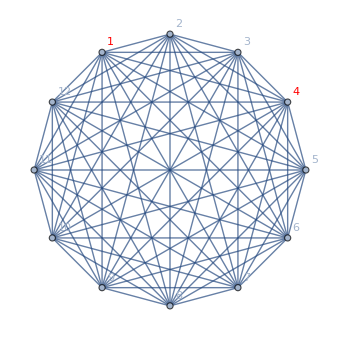
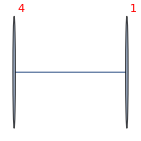
{-Graphics-,-Graphics-}vertices:12, non-edges:36, taken:12, not-taken:24

```mathematica
SolGraph[Graph[plantri [[1]] ],v19bx25cx37ax468,{1,2,3,4},{1,4}]
```

```mathematica
Clear[MpgChain2]
```

```mathematica
SymbolToColoring[First[FindFullFormula4[Graph[plantri [[1]] ]]]]
```

{1→RGBColor[1, 0, 0],9→RGBColor[1, 0, 0],11→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],12→RGBColor[0, 0, 1],3→RGBColor[1, 1, 0],7→RGBColor[1, 1, 0],10→RGBColor[1, 1, 0],4→RGBColor[0, 1, 0],6→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0]}

```mathematica
MpgChain2[g_,glayout_:"TutteEmbedding",previous_:{}, positions_:Null,size_:{}, highlight_:{}]:=Block[{contract, result, coord, newPos=positions,newSize=size, layout, thegraph,form,graphs,first,newNeighbors},
If[VertexCount[g]==4,Return[{}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
If[positions==Null,
layout = Graph[
SortGraph[g],
GraphLayout->glayout,
GraphHighlightStyle->"Thick",
ImageSize->{6 cm,6 cm}, 
VertexCoordinates->Automatic
];
newPos=First[AbsoluteOptions[layout, VertexCoordinates]][[2]];
newSize=First[AbsoluteOptions[layout, ImageSize]][[2]];
];
coord=newPos;(*Table[newPos[[k]],{k,VertexList[g]}];*)
form=FindFullFormula4[g];
newNeighbors=Intersection[VertexList[NeighborhoodGraph[g,e[[1]]]],VertexList[NeighborhoodGraph[g,e[[2]]]]];
If[form≠{},first=First[form];form=SymbolToColoring[first]];
thegraph=Graph[
Range[Length[newPos]],
EdgeList[g],
GraphHighlightStyle->"Thick",
VertexLabels->Map[If[MemberQ[highlight,#[[1]]],#[[1]]->Style[#[[2]],Directive[Red,Underlined]],#]&,Map[If[MemberQ[newNeighbors,#],#->Framed[#],If[MemberQ[previous,#],#->ToString[previous],#->#]]&,VertexList[g]]],
GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],
VertexLabelStyle->Directive[Darker[Green],Italic,10],
ImageSize->newSize, 
AspectRatio->1,
EdgeStyle->{e->{Thick,Blue,Dashed}}, 
VertexStyle->form, 
VertexSize->Map[#->If[MemberQ[previous,#],Larger[Large],Large]&,VertexList[g]],
VertexCoordinates->coord
];
result=Prepend[MpgChain2[contract,glayout,{e[[1]],e[[2]]}, newPos,newSize,newNeighbors],{Labeled[
thegraph,{Column[ExplainContractionCounts[g,e]],Style[ChromaticPolynomial[g,4]/24,Green ],Grid[Transpose[Map[{#,VertexDegree[g,#]}&,Sort[VertexList[g]]]],Frame->All]}],
Labeled[SolGraph[g,first,newNeighbors, highlight],highlight],
graphs=Table[
With[{sub=NeighborhoodGraph[ thegraph,v]},
Graph[EdgeList[sub],VertexSize->Medium,GraphLayout->"SpringElectricalEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",EdgeStyle->{e->{Thick,Blue,Dashed}},ImageSize->{3 cm,3 cm}]
],
{v,{e[[1]],e[[2]]}}
];
With[
{sub=GraphUnion[graphs[[1]],graphs[[2]]]},
Labeled[Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",EdgeStyle->{e->{Thick,Blue,Dashed}},ImageSize->{4 cm,4 cm}],e]]

,

Column[
With[
{sub=NeighborhoodGraph[VertexContract[ thegraph,e],e[[1]]]},
{
Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",ImageSize->{4 cm,4 cm}]
,
form=FindFullFormula4[sub];
If[form≠{},form=SymbolToColoring[First[form]]];
Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",ImageSize->{4 cm,4 cm}]
}]
]}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

## experiments come

```mathematica
FindFullFormula4[VertexContract[Graph[plantri [[1]] ],{1,2}]]
```

{v19bx37ax468x5c,v19bx37ax46cx58,v1cx36ax48bx579,v1ax36cx48bx579,v19bx357x4cx68a,v19bx35cx47x68a,v19bx357x46cx8a,v19bx35cx468x7a}

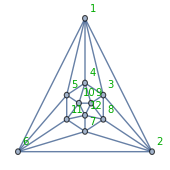
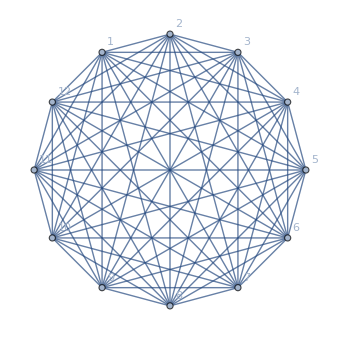
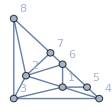
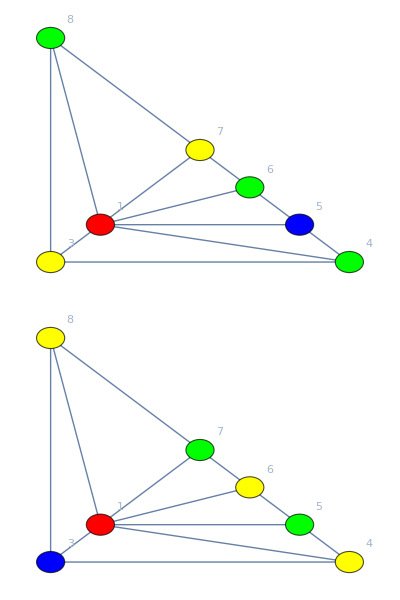
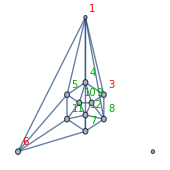
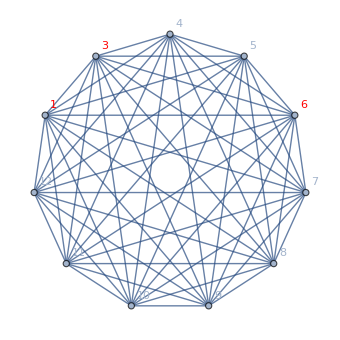
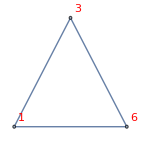
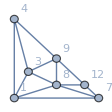
{{-Graphics-{4
24,10,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5},{-Graphics-,-Graphics-}vertices:12, non-edges:36, taken:12, not-taken:24{},-Graphics-1<->2,-Graphics-},{-Graphics-{4
17,8,1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
6 | 4 | 5 | 5 | 4 | 5 | 5 | 5 | 5 | 5 | 5},{-Graphics-,-Graphics-}vertices:11, non-edges:28, taken:10, not-taken:18{1,2,3,6},-Graphics-3<->8,-Graphics-},{-Graphics-{3
12,8,1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 11 | 12
5 | 5 | 5 | 5 | 4 | 5 | 4 | 5 | 5 | 5},{-Graphics-,-Graphics-}vertices:10, non-edges:21, taken:8, not-taken:13{1,3,8,9},-Graphics-4<->9,-Graphics-},{-Graphics-{2
8,2,1 | 3 | 4 | 5 | 6 | 7 | 10 | 11 | 12
5 | 4 | 5 | 5 | 4 | 5 | 4 | 5 | 5},{-Graphics-,-Graphics-}vertices:9, non-edges:15, taken:6, not-taken:9{3,4,9,10},-Graphics-5<->10,-Graphics-},{-Graphics-{2
4,3,1 | 3 | 4 | 5 | 6 | 7 | 11 | 12
5 | 4 | 4 | 5 | 4 | 5 | 4 | 5},{-Graphics-,-Graphics-}vertices:8, non-edges:10, taken:4, not-taken:6{4,5,10,11},-Graphics-6<->11,-Graphics-},{-Graphics-{0
3,5,1 | 3 | 4 | 5 | 6 | 7 | 12
5 | 4 | 4 | 4 | 4 | 4 | 5},{-Graphics-,-Graphics-}vertices:7, non-edges:6, taken:3, not-taken:3{5,6,7,11},-Graphics-7<->12,-Graphics-},{-Graphics-{0
1,1,1 | 3 | 4 | 5 | 6 | 7
5 | 3 | 4 | 4 | 3 | 5},{-Graphics-,-Graphics-}vertices:6, non-edges:3, taken:2, not-taken:1{3,6,7,12},-Graphics-3<->1,-Graphics-},{-Graphics-{0
0,1,1 | 4 | 5 | 6 | 7
4 | 3 | 4 | 3 | 4},{-Graphics-,-Graphics-}vertices:5, non-edges:1, taken:1, not-taken:0{1,3,4,7},-Graphics-5<->4,-Graphics-}}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```

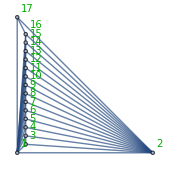
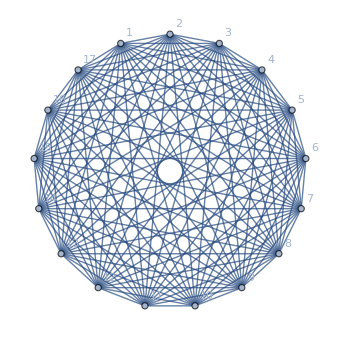
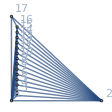
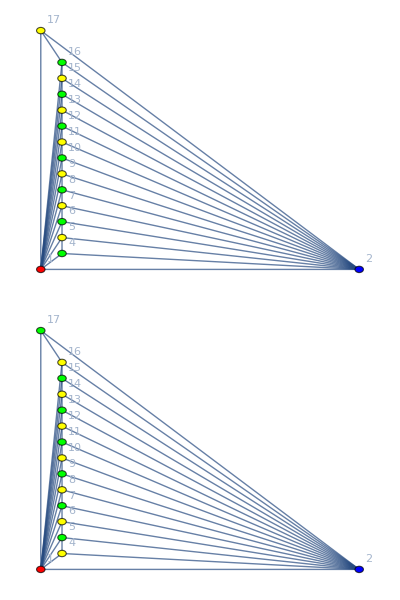
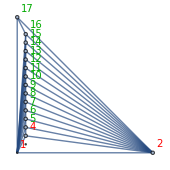
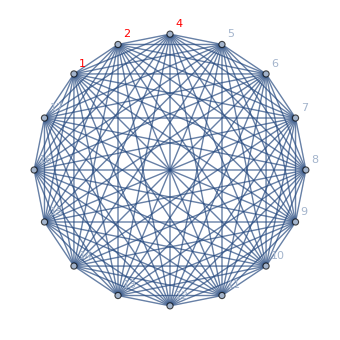
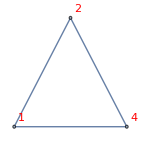
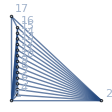
{{-Graphics-{0
78,1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
16 | 16 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:17, non-edges:91, taken:49, not-taken:42{},-Graphics-1<->3,-Graphics-},{-Graphics-{0
66,1,1 | 2 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
15 | 15 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:16, non-edges:78, taken:42, not-taken:36{1,2,3,4},-Graphics-2<->4,-Graphics-},{-Graphics-{10
45,1,1 | 2 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
14 | 14 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:15, non-edges:66, taken:36, not-taken:30{1,2,4,5},-Graphics-5<->6,-Graphics-},{-Graphics-{8
37,1,1 | 2 | 5 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
13 | 13 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:14, non-edges:55, taken:30, not-taken:25{1,2,5,6},-Graphics-7<->8,-Graphics-},{-Graphics-{7
29,1,1 | 2 | 5 | 7 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
12 | 12 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:13, non-edges:45, taken:25, not-taken:20{1,2,7,8},-Graphics-9<->10,-Graphics-},{-Graphics-{6
22,1,1 | 2 | 5 | 7 | 9 | 11 | 12 | 13 | 14 | 15 | 16 | 17
11 | 11 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:12, non-edges:36, taken:20, not-taken:16{1,2,9,10},-Graphics-11<->12,-Graphics-},{-Graphics-{5
16,1,1 | 2 | 5 | 7 | 9 | 11 | 13 | 14 | 15 | 16 | 17
10 | 10 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:11, non-edges:28, taken:16, not-taken:12{1,2,11,12},-Graphics-13<->14,-Graphics-},{-Graphics-{4
11,1,1 | 2 | 5 | 7 | 9 | 11 | 13 | 15 | 16 | 17
9 | 9 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:10, non-edges:21, taken:12, not-taken:9{1,2,13,14},-Graphics-15<->16,-Graphics-},{-Graphics-{0
10,1,1 | 2 | 5 | 7 | 9 | 11 | 13 | 15 | 17
8 | 8 | 3 | 4 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:9, non-edges:15, taken:9, not-taken:6{1,2,15,16},-Graphics-1<->17,-Graphics-},{-Graphics-{0
6,1,1 | 2 | 5 | 7 | 9 | 11 | 13 | 15
7 | 7 | 3 | 4 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:8, non-edges:10, taken:6, not-taken:4{1,2,15,17},-Graphics-5<->2,-Graphics-},{-Graphics-{2
1,1,1 | 2 | 7 | 9 | 11 | 13 | 15
6 | 6 | 3 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:7, non-edges:6, taken:4, not-taken:2{1,2,5,7},-Graphics-9<->7,-Graphics-},{-Graphics-{0
1,1,1 | 2 | 7 | 11 | 13 | 15
5 | 5 | 3 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:6, non-edges:3, taken:2, not-taken:1{1,2,7,9},-Graphics-13<->11,-Graphics-},{-Graphics-{0
0,1,1 | 2 | 7 | 11 | 15
4 | 4 | 3 | 4 | 3},{-Graphics-,-Graphics-}vertices:5, non-edges:1, taken:1, not-taken:0{1,2,11,13},-Graphics-1<->15,-Graphics-}}

```mathematica
MpgChain2[MinimalGraph[16] ,"PlanarEmbedding"]
```

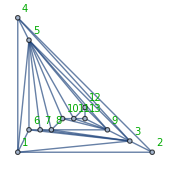
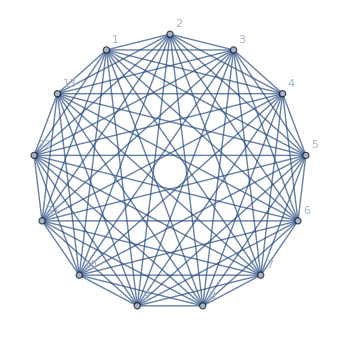
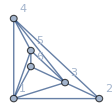
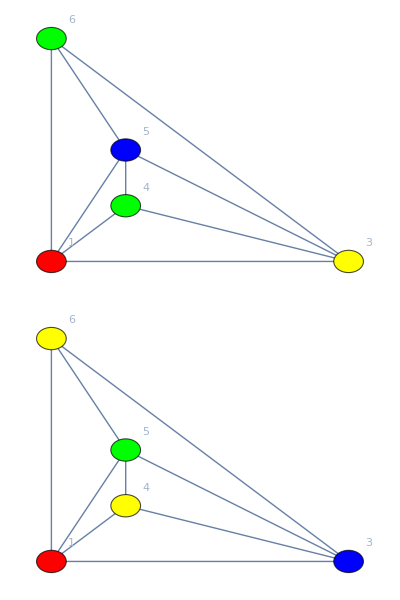
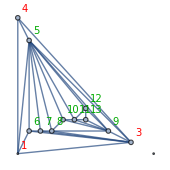
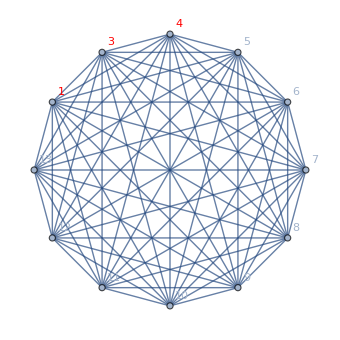
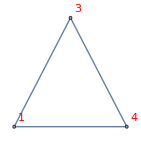
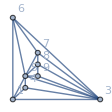
{{-Graphics-{7
29,1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 3 | 8 | 4 | 10 | 4 | 4 | 5 | 7 | 4 | 5 | 4 | 3},{-Graphics-,-Graphics-}vertices:13, non-edges:45, taken:15, not-taken:30{},-Graphics-1<->2,-Graphics-},{-Graphics-{4
24,1,1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
4 | 7 | 3 | 10 | 4 | 4 | 5 | 7 | 4 | 5 | 4 | 3},{-Graphics-,-Graphics-}vertices:12, non-edges:36, taken:13, not-taken:23{1,2,3,4},-Graphics-3<->4,-Graphics-},{-Graphics-{5
16,1,1 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
3 | 6 | 9 | 4 | 4 | 5 | 7 | 4 | 5 | 4 | 3},{-Graphics-,-Graphics-}vertices:11, non-edges:28, taken:10, not-taken:18{1,3,4,5},-Graphics-6<->7,-Graphics-},{-Graphics-{3
12,1,1 | 3 | 5 | 6 | 8 | 9 | 10 | 11 | 12 | 13
3 | 5 | 8 | 4 | 5 | 7 | 4 | 5 | 4 | 3},{-Graphics-,-Graphics-}vertices:10, non-edges:21, taken:8, not-taken:13{3,5,6,7},-Graphics-8<->10,-Graphics-},{-Graphics-{0
10,1,1 | 3 | 5 | 6 | 8 | 9 | 11 | 12 | 13
3 | 5 | 7 | 4 | 5 | 6 | 5 | 4 | 3},{-Graphics-,-Graphics-}vertices:9, non-edges:15, taken:6, not-taken:9{5,8,9,10},-Graphics-5<->12,-Graphics-
-Graphics-},{-Graphics-{2
4,1,1 | 3 | 5 | 6 | 8 | 9 | 11 | 13
3 | 5 | 7 | 4 | 5 | 5 | 4 | 3},{-Graphics-,-Graphics-}vertices:8, non-edges:10, taken:5, not-taken:5{5,9,11,12},-Graphics-9<->13,-Graphics-
-Graphics-},{-Graphics-{1
2,1,1 | 3 | 5 | 6 | 8 | 9 | 11
3 | 5 | 6 | 4 | 5 | 4 | 3},{-Graphics-,-Graphics-}vertices:7, non-edges:6, taken:3, not-taken:3{5,9,11,13},-Graphics-3<->1,-Graphics-
-Graphics-},{-Graphics-{0
1,1,1 | 5 | 6 | 8 | 9 | 11
4 | 5 | 3 | 5 | 4 | 3},{-Graphics-,-Graphics-}vertices:6, non-edges:3, taken:2, not-taken:1{1,3,5,6},-Graphics-8<->6,-Graphics-
-Graphics-},{-Graphics-{0
0,1,1 | 5 | 6 | 9 | 11
3 | 4 | 4 | 4 | 3},{-Graphics-,-Graphics-}vertices:5, non-edges:1, taken:1, not-taken:0{1,5,6,8},-Graphics-5<->11,-Graphics-
-Graphics-}}

```mathematica
MpgChain2[MinimalGraph2[12] ,"PlanarEmbedding"]
```